```mathematica
ArcCos[0.707107]
```

0.785398

```mathematica
Cos[2 I]
```

Cosh[2]

```mathematica
N[Cos[2 I]]
```

3.7622

```mathematica
N[Cosh[2]]
```

3.7622

```mathematica
fes[x_]=(1/2)*(Exp[-x] + Exp[x])
```

1/2 (ⅇ^-x+ⅇ^x)

```mathematica
fes[2]
```

1/2 (1/ⅇ^2+ⅇ^2)

```mathematica
fes[2.]
```

3.7622

```mathematica
Cos[2.* I]
```

3.7622+0. ⅈ

```mathematica
Cosh[2.]
```

3.7622

```mathematica
(*--------------------------------------------------------*)
```

```mathematica
a= -5 + I;
b= 1+2 I;
Log[a b] === Log[a] + Log[b]
```

False

```mathematica
(* a e b sono complessi, il prodotto è definito diversamente, la proprietà del logaritmo non vale più *)
```

```mathematica
z=x+I y;
Plot3D[Im[Log[z]], {x,-3,3}, {y,-3,3}]
```

-Graphics3D-

```mathematica
(*--------------------------------------------------------*)
```

```mathematica
f[k_]= k^(1/2);
ParametricPlot3D[ {Re[f[u+I v]],Im[f[u+I v]],Re[f[u+I v]]+Im[f[u+I v]]}  ,{u,-10,10}, {v,-10,10}]
```

-Graphics3D-

```mathematica
Plot3D[Re[f[x+I y]]+Im[f[x +I y]],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
(*--------------------------------------------------------*)
```

```mathematica
??Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

Attributes[Integrate]={Protected,ReadProtected}
 
Options[Integrate]:={Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
Integrate[ 1/((1-2*(Sin[x]^2))^(1/2)), x]
```

EllipticF[x,2]

```mathematica
Integrate[ x Exp[-x^2], {x,0,Infinity}]
```

1/2

```mathematica
Integrate[ (1/Pi) (Cos[ ((x^3)/3) + x t ]) ,{x,0,Infinity}]
```

ConditionalExpression[AiryAi[t],t∈ℝ]

```mathematica
(*--------------------------------------------------------*)

Clear[a,b,f]
```

```mathematica
(*algoritmo per calcolare il determinante di una 3x3 conoscendo l'espressione del det di una 2x2*)
```

```mathematica
MatrixForm[{{a,b},{c,d}}]
```

(a | b
c | d)

```mathematica
Det[{{a,b},{c,d}}]
```

-b c+a d

```mathematica
MatrixForm[{{a11,b12,e13},{c21,d22,f23}, {g31,h32,i33}}]
```

(a11 | b12 | e13
c21 | d22 | f23
g31 | h32 | i33)

```mathematica
M2={{a,b},{c,d}};
M3={{a,b,e},{c,d,f}, {g,h,i}};

fdet2[i_,j_]=M3[[i,j]]*M3[[i+1,j+1]]  - M3[[i,j+1]]*M3[[i+1,j]] ; 

fdet3=Sum[ (-1^(i+j))*M3[[i,j]]*fdet2[i,j] ,{i,1,3},{j,1,3}]
```

-a (-b c+a d)[1,1]-b (-b c+a d)[1,2]-e (-b c+a d)[1,3]-c (-b c+a d)[2,1]-d (-b c+a d)[2,2]-f (-b c+a d)[2,3]-g (-b c+a d)[3,1]-h (-b c+a d)[3,2]-3 (-b c+a d)[3,3]

```mathematica
Clear[z,z1]
(*--------------------------------------------------------*)
```

```mathematica
eq11= x +3 y + 5 z==7;
eq12= x + 2 y + 4 z == 6;
eq13 = x + y+ z == 5;

Solve[{eq11,eq12,eq13},{x,y,z}]
```

{{x→4,y→1,z→0}}

```mathematica
eq21= x +3 y + 5 z;
eq22= x + 2 y + 4 z;
eq23 = x + y+ z ;
coeff={0,0,0};

Solve[{eq21==0, eq22==0, eq23==0},{x,y,z}]
Solve[{eq21,eq22,eq23}==coeff ,{x,y,z}]
```

{{x→0,y→0,z→0}}

{{x→0,y→0,z→0}}

```mathematica
eq31=x+2 y +3 z == 7;
eq32=4 x + 5 y + 6 z ==6;
eq33=7 x +8 y + 9 z ==5;
Solve[{eq31,eq32,eq33},{x,y,z}]
```

{{y→-8-2 x,z→23/3+x}}

```mathematica
eq41=x+2 y +3 z == 0;
eq42=4 x + 5 y + 6 z ==0;
eq43=7 x +8 y + 9 z ==0;
Solve[{eq41,eq42,eq43},{x,y,z}]
```

{{y→-2 x,z→x}}

```mathematica
eq31=x+2 y +3 z ;
eq32=4 x + 5 y + 6 z ;
eq33=7 x +8 y + 9 z ;
coeff3={7,6,5};

Solve[{eq31,eq32,eq33}==coeff3,{x,y,z}]
```

{{y→-8-2 x,z→23/3+x}}

```mathematica
Clear[eq,eq11,eq12,eq13,eq21,eq22,eq23,eq31,eq32,eq33,eq41,eq42,eq43,coeff,coeff3,x,y]
(*--------------------------------------------------------*)
```

```mathematica
eq= x+y -z==-1;
eq2=x^2 + y^2 -z==3 ;
z1=z /. Solve[eq ,z];
z2=z /. Solve[eq2 ,z];
Plot[{z1,z2},{x,-5,5},{y,-5,5}]
```

```mathematica
Plot3D[{z1,z2},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
solsist=Solve[{eq,eq2},{y,z}]
```

{{y→1/2 (1-√(17+4 x-4 x^2)),z→1/2 (3+2 x-√(17+4 x-4 x^2))},{y→1/2 (1+√(17+4 x-4 x^2)),z→3/2+x+1/2 √(17+4 x-4 x^2)}}

```mathematica
sol1=y/.solsist
```

{1/2 (1-√(17+4 x-4 x^2)),1/2 (1+√(17+4 x-4 x^2))}

```mathematica
Cases[%14,Sqrt[_],Infinity]
```

{√(17+4 x-4 x^2),√(17+4 x-4 x^2)}

```mathematica
Union[Cases[%20,Sqrt[_],Infinity]]
```

{√(17+4 x-4 x^2)}

```mathematica
Union[Cases[%20,Sqrt[_],Infinity]][[1,1]]
```

17+4 x-4 x^2

```mathematica
eqdelta= %
```

17+4 x-4 x^2

```mathematica
x1:=x/.Solve[eqdelta==0,x][[1]];
x2:=x/.Solve[eqdelta==0,x][[2]]
```

```mathematica
Print["Intervallo: x ∈ [  " , x1 , "  ,  " , x2, "  ]"]
```

Intervallo: x ∈ [  1/2 (1-3 √2)  ,  1/2 (1+3 √2)  ]

```mathematica
solsist=Solve[{eq,eq2},{y,z}]
```

{{y→1/2 (1-√(17+4 x-4 x^2)),z→1/2 (3+2 x-√(17+4 x-4 x^2))},{y→1/2 (1+√(17+4 x-4 x^2)),z→3/2+x+1/2 √(17+4 x-4 x^2)}}

```mathematica
f1={y,z}/.solsist[[1]]
```

{1/2 (1-√(17+4 x-4 x^2)),1/2 (3+2 x-√(17+4 x-4 x^2))}

```mathematica
f2={y,z}/.solsist[[2]]
```

{1/2 (1+√(17+4 x-4 x^2)),3/2+x+1/2 √(17+4 x-4 x^2)}

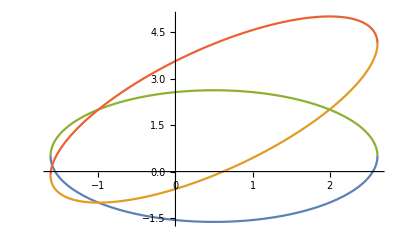

```mathematica
Plot[{f1, f2}, {x,x1,x2}]
```

```mathematica
(*--------------------------------------------------------*)
```

```mathematica
int[r_,s_]=Integrate[(t^(r-1)) ((1-t)^(s-1)),{t,1,0}]
```

ConditionalExpression[-(Gamma[r] Gamma[s])/Gamma[r+s],Re[r]>0&&Re[s]>0]

```mathematica
??Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

Attributes[Integrate]={Protected,ReadProtected}
 
Options[Integrate]:={Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
int1[r_,s_]=Integrate[(t^(r-1)) ((1-t)^(s-1)),{t,1,0}, GenerateConditions->False]
```

-(Gamma[r] Gamma[s])/Gamma[r+s]

```mathematica
Manipulate[Plot[-(Gamma[r] Gamma[s])/Gamma[r+s],{r,-10.,10.}],{s,-10.,10.}]
```

```mathematica
(*--------------------------------------------------------*)
```

```mathematica
hermite[n_,x_]:=Simplify[ Exp[x^2]*(D[  Exp[-((x-t)^2)]  ,{t,n}]/.t->0)]
```

```mathematica
hermite[13,k]
```

128 k (135135-540540 k^2+540540 k^4-205920 k^6+34320 k^8-2496 k^10+64 k^12)

```mathematica
hermi[0,x_]=1;
hermi[1,x_]=2x;
hermi[n_,x_]:=Simplify[2 x hermi[n-1,x] - 2 n hermi[n-2,x]]
```

```mathematica
hermi[20,x]
```

2048 (1857945600-27125492625 x^2+62670935250 x^4-53632378800 x^6+22205383200 x^8-5026301280 x^10+659305920 x^12-50983680 x^14+2271744 x^16-53504 x^18+512 x^20)

```mathematica
M=Table[hermi[i,x],{i,1,20}]//MatrixForm
```

(2 x
4 (-1+x^2)
4 x (-5+2 x^2)
8 (4-9 x^2+2 x^4)
8 x (33-28 x^2+4 x^4)
16 (-24+87 x^2-40 x^4+4 x^6)
16 x (-279+370 x^2-108 x^4+8 x^6)
32 (192-975 x^2+690 x^4-140 x^6+8 x^8)
32 x (2895-5280 x^2+2352 x^4-352 x^6+16 x^8)
64 (-1920+12645 x^2-12180 x^4+3752 x^6-432 x^8+16 x^10)
64 x (-35685+83370 x^2-50232 x^4+11376 x^6-1040 x^8+32 x^10)
128 (23040-187425 x^2+229530 x^4-95256 x^6+16560 x^8-1232 x^10+32 x^12)
128 x (509985-1458660 x^2+1112076 x^4-338400 x^6+46640 x^8-2880 x^10+64 x^12)
256 (-322560+3133935 x^2-4672080 x^4+2445660 x^6-570240 x^8+63888 x^10-3328 x^12+64 x^14)
256 x (-8294895+28147770 x^2-26025300 x^4+9967320 x^6-1840080 x^8+170976 x^10-7616 x^12+128 x^14)
512 (5160960-58437855 x^2+102901050 x^4-65155860 x^6+19091160 x^8-2862288 x^10+224224 x^12-8640 x^14+128 x^16)
512 x (151335135-595387800 x^2+648232200 x^4-299756160 x^6+69463680 x^8-8631168 x^10+577920 x^12-19456 x^14+256 x^16)
1024 (-92897280+1203216525 x^2-2447606700 x^4+1821037680 x^6-643397040 x^8+120984864 x^10-12667200 x^12+733440 x^14-21760 x^16+256 x^18)
1024 x (-3061162125+13718801250 x^2-17211625200 x^4+9337442400 x^6-2606604000 x^8+405961920 x^10-36314880 x^12+1836544 x^14-48384 x^16+512 x^18)
2048 (1857945600-27125492625 x^2+62670935250 x^4-53632378800 x^6+22205383200 x^8-5026301280 x^10+659305920 x^12-50983680 x^14+2271744 x^16-53504 x^18+512 x^20))

```mathematica
ps[i_,j_]:=Integrate[hermi[i,x] hermi[j,x]  (-2 x Exp[-x^2]),
{x,-(Infinity),Infinity}];
check=Table[ps[i,j], {i,1,20},{j,1,20}]//MatrixForm
```

(0 | -4 √π | 0 | 32 √π | 0 | -288 √π | 0 | 3072 √π | 0 | -38400 √π | 0 | 552960 √π | 0 | -9031680 √π | 0 | 165150720 √π | 0 | -3344302080 √π | 0 | 74317824000 √π
-4 √π | 0 | -32 √π | 0 | 288 √π | 0 | -3072 √π | 0 | 38400 √π | 0 | -552960 √π | 0 | 9031680 √π | 0 | -165150720 √π | 0 | 3344302080 √π | 0 | -74317824000 √π | 0
0 | -32 √π | 0 | -224 √π | 0 | 2688 √π | 0 | -35328 √π | 0 | 522240 √π | 0 | -8663040 √π | 0 | 159989760 √π | 0 | -3261726720 √π | 0 | 72831467520 √π | 0 | -1768764211200 √π
32 √π | 0 | -224 √π | 0 | -2304 √π | 0 | 32256 √π | 0 | -491520 √π | 0 | 8294400 √π | 0 | -154828800 √π | 0 | 3179151360 √π | 0 | -71345111040 √π | 0 | 1739037081600 √π | 0
0 | 288 √π | 0 | -2304 √π | 0 | -26880 √π | 0 | 442368 √π | 0 | -7741440 √π | 0 | 147456000 √π | 0 | -3065610240 √π | 0 | 69363302400 √π | 0 | -1700391813120 √π | 0 | 44947419955200 √π
-288 √π | 0 | 2688 √π | 0 | -26880 √π | 0 | -374784 √π | 0 | 7004160 √π | 0 | -137871360 √π | 0 | 2921103360 √π | 0 | -66886041600 √π | 0 | 1652828405760 √π | 0 | -43936697548800 √π | 0
0 | -3072 √π | 0 | 32256 √π | 0 | -374784 √π | 0 | -5935104 √π | 0 | 124600320 √π | 0 | -2727936000 √π | 0 | 63665602560 √π | 0 | -1592383242240 √π | 0 | 42676267253760 √π | 0 | -1222855203225600 √π
3072 √π | 0 | -35328 √π | 0 | 442368 √π | 0 | -5935104 √π | 0 | -106168320 √π | 0 | 2468413440 √π | 0 | -59454259200 √π | 0 | 1515092705280 √π | 0 | -41094783959040 √π | 0 | 1187182647705600 √π | 0
0 | 38400 √π | 0 | -491520 √π | 0 | 7004160 √π | 0 | -106168320 √π | 0 | -2110095360 √π | 0 | 53827338240 √π | 0 | -1414515916800 √π | 0 | 39081266380800 √π | 0 | -1142591953305600 √π | 0 | 35395736489164800 √π
-38400 √π | 0 | 522240 √π | 0 | -7741440 √π | 0 | 124600320 √π | 0 | -2110095360 √π | 0 | -46183219200 √π | 0 | 1281734737920 √π | 0 | -36485097062400 √π | 0 | 1086229315584000 √π | 0 | -34051594597171200 √π | 0
0 | -552960 √π | 0 | 8294400 √π | 0 | -137871360 √π | 0 | 2468413440 √π | 0 | -46183219200 √π | 0 | -1103230402560 √π | 0 | 33086295244800 √π | 0 | -1014051844915200 √π | 0 | 32362142367744000 √π | 0 | -1082847557320704000 √π
552960 √π | 0 | -8663040 √π | 0 | 147456000 √π | 0 | -2727936000 √π | 0 | 53827338240 √π | 0 | -1103230402560 √π | 0 | -28565789736960 √π | 0 | 920351932416000 √π | 0 | -30213227623219200 √π | 0 | 1028876407721164800 √π | 0
0 | 9031680 √π | 0 | -154828800 √π | 0 | 2921103360 √π | 0 | -59454259200 √π | 0 | 1281734737920 √π | 0 | -28565789736960 √π | 0 | -796865436057600 √π | 0 | 27444086046720000 √π | 0 | -960641943522508800 √π | 0 | 34767968003319398400 √π
-9031680 √π | 0 | 159989760 √π | 0 | -3065610240 √π | 0 | 63665602560 √π | 0 | -1414515916800 √π | 0 | 33086295244800 √π | 0 | -796865436057600 √π | 0 | -23825462014771200 √π | 0 | 873315527609548800 √π | 0 | -32466249153773568000 √π | 0
0 | -165150720 √π | 0 | 3179151360 √π | 0 | -66886041600 √π | 0 | 1515092705280 √π | 0 | -36485097062400 √π | 0 | 920351932416000 √π | 0 | -23825462014771200 √π | 0 | -760072762294272000 √π | 0 | 29538999201064550400 √π | 0 | -1162208434276270080000 √π
165150720 √π | 0 | -3261726720 √π | 0 | 69363302400 √π | 0 | -1592383242240 √π | 0 | 39081266380800 √π | 0 | -1014051844915200 √π | 0 | 27444086046720000 √π | 0 | -760072762294272000 √π | 0 | -25769717125034803200 √π | 0 | 1058271506687066112000 √π | 0
0 | 3344302080 √π | 0 | -71345111040 √π | 0 | 1652828405760 √π | 0 | -41094783959040 √π | 0 | 1086229315584000 √π | 0 | -30213227623219200 √π | 0 | 873315527609548800 √π | 0 | -25769717125034803200 √π | 0 | -925303716900451123200 √π | 0 | 40032746800316153856000 √π
-3344302080 √π | 0 | 72831467520 √π | 0 | -1700391813120 √π | 0 | 42676267253760 √π | 0 | -1142591953305600 √π | 0 | 32362142367744000 √π | 0 | -960641943522508800 √π | 0 | 29538999201064550400 √π | 0 | -925303716900451123200 √π | 0 | -35077176116436271104000 √π | 0
0 | -74317824000 √π | 0 | 1739037081600 √π | 0 | -43936697548800 √π | 0 | 1187182647705600 √π | 0 | -34051594597171200 √π | 0 | 1028876407721164800 √π | 0 | -32466249153773568000 √π | 0 | 1058271506687066112000 √π | 0 | -35077176116436271104000 √π | 0 | -1399960389114711244800000 √π
74317824000 √π | 0 | -1768764211200 √π | 0 | 44947419955200 √π | 0 | -1222855203225600 √π | 0 | 35395736489164800 √π | 0 | -1082847557320704000 √π | 0 | 34767968003319398400 √π | 0 | -1162208434276270080000 √π | 0 | 40032746800316153856000 √π | 0 | -1399960389114711244800000 √π | 0)

```mathematica
Clear[y,n](*-----------------------------------------------------*)
```

```mathematica
eqh = y''[x] + (2 n +1 - x^2) y[x]==0;
sol[k_]= y[x]/.DSolve[eqh,y[x],x]
```

{C[2] ParabolicCylinderD[-1-n,ⅈ √2 x]+C[1] ParabolicCylinderD[n,√2 x]}

```mathematica
solf2= sol[x]/.{C[2]->1,C[1]->0}
```

{ParabolicCylinderD[-1-n,ⅈ √2 x]}

```mathematica
Plot[Exp[(-1/2) x^2] solf2 /. n->1, {x,-5,5}]
```

-Graphics-

```mathematica
Plot[Exp[(-1/2) x^2] solf2 /. n->2, {x,-5,5}]
```

-Graphics-

```mathematica
Clear[y]
(*-----------------------------------------------------*)
```

```mathematica
sol[p_]=h[x]/.DSolve[{h''[x] - x h[x] ==0 ,h'[0]==1, h[0]==0}, h[x],x]
```

{1/6 (-3 3^(1/3) AiryAi[x] Gamma[1/3]+3^(5/6) AiryBi[x] Gamma[1/3])}